# Zaporedja in njihove limite

### Naloge:

#### 1. naloga:

Poišči limito danega zaporedja:

Prvo zaporedje zapišemo v obliki, ki jo bo program mathematica razumel.

```mathematica
Zaporedje1[n_] := (6*n - 5*Cos[(n*Pi)/2] )/(2*n - 1 )
```

Da bomo imeli predstavo o limiti, si bomo zapisali prvih nekaj členov zaporedja:

```mathematica
Map[Zaporedje1,Range[8]]
```

{6,17/3,18/5,19/7,10/3,41/11,42/13,43/15}

Opazimo, da zaporedje niti ne narašča niti ne pada, toda se njegovi členi približujejo številu 3.
Naslednji korak bo, da narišemo graf, tako da se prepričamo, da se členi zaporedja res približujejo številu 3.

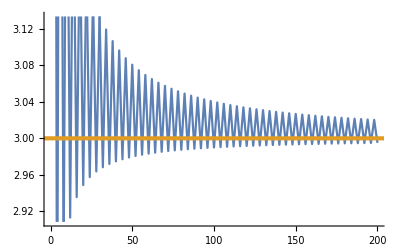

```mathematica
ListLinePlot[Map[Zaporedje1,Range[200]],GridLines->{None,{3}},GridLinesStyle->Directive[AbsoluteThickness[6/2], ColorData[97,2]]]
```

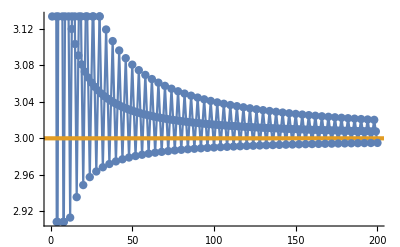

```mathematica
ListLinePlot[Map[Zaporedje1,Range[200]],Mesh->All,GridLines->{None,{3}},GridLinesStyle->Directive[AbsoluteThickness[6/2], ColorData[97,2]]]
```

Iz obeh grafov je razvidno da se zaporedje priblizuje številu 3. Če bi graf podaljšali v neskončnost, bi pri premici y=3 točke zaporedja bile čisto zgoščene.
Od tod sledi, da je naša limita najvrjetneje 3, sedaj bomo to še pokazali z uporabo funkcije limit.

```mathematica
Limit[(6*n - 5*Cos[(n*Pi)/2] )/(2*n - 1 ),n-> Infinity]
```

3

Pokazali smo, da je limita našega zaporedja število 3.

#### 2. Naloga

Določi limito zaporedja v kompleksni ravnini.

Kakor prej, bomo prvo zaporedje zapisali v obliki, da ga bo naš program razumel.

```mathematica
Zaporedje2[n_]:=(1/n)*(Cos[(n*Pi)/2] +I* Sin[(n*Pi)/2] )
```

Sedaj bomo napisali prvih nekaj členov zaporedja.

```mathematica
Map[Zaporedje2,Range[8]]
```

{ⅈ,-1/2,-ⅈ/3,1/4,ⅈ/5,-1/6,-ⅈ/7,1/8}

Opazimo, da zaporedje pada, členi se razvidno približujejo 0.
Naslednji korak bo, da narišemo graf, tako da se prepričamo, da se členi zaporedja res približujejo številu 0.

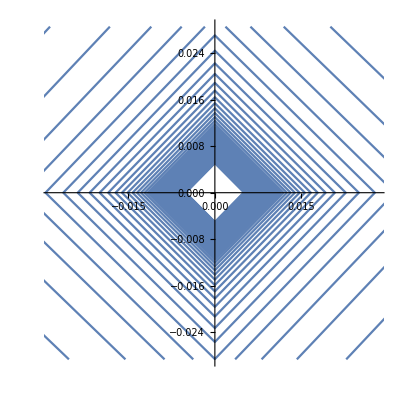

```mathematica
ListLinePlot[(Tooltip[{Re[#1],Im[#1]}]&)/@Map[Zaporedje2,Range[200]],AspectRatio->1]
```

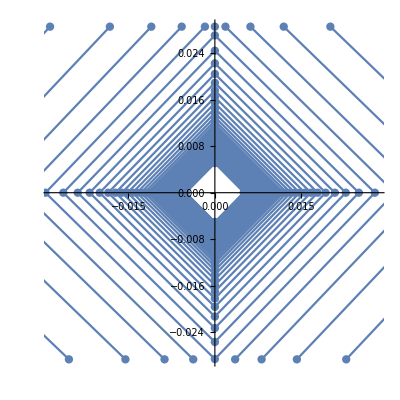

```mathematica
ListLinePlot[(Tooltip[{Re[#1],Im[#1]}]&)/@Map[Zaporedje2,Range[200]],AspectRatio->1,Mesh->All]
```

Glede na to, da je enota na grafu 0.01, lahko vidimo, da se zaporedje zelo počasi približuje številu 0.
Probamo še funkcijo Limit pri našem zaporedju in opazili bomo, da je limita res enaka 0.

```mathematica
Limit[(1/n)*(Cos[(n*Pi)/2] +I* Sin[(n*Pi)/2] ),n->Infinity]
```

0

Pokazali smo, da je limita našega zaporedja število 0.

#### 3. Naloga:

Poišči limito zaporedja.

Sedaj je naše zaporedje bolj podobno vrsti, zato bomo morali uporabiti izrek o sendviču.

-Graphics-

Da sploh lahko uporabimo izrek o sendviču bomo morali naše zaporedje oceniti.

Opazimo, da je vsak člen zaporedja manjši od zaporedja: -Graphics-  Poimenujmo ga Bn.

Seveda, da bi lahko naredili izrek o sendviču, moramo najti tudi zaporedje od katerega členi bodo vedno manjši od naših členov.
Zaporedje, ki je takšno, je -Graphics-. Poimenujmo ga Cn.
Če bosta limiti zaporedij Bn in Cn enaki, bomo lahko po izreku o sendču sklepali, da je tudi limita našega zaporedja enaka limitam Bn in Cn

Sedaj pa preverimo limiti Bn in Cn.

1. Limita Bn je:

```mathematica
Bn[n_]:=n/Sqrt[n^2 + 1]
```

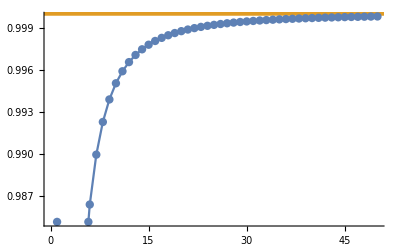

```mathematica
ListLinePlot[Map[Bn,Range[50]],Mesh->All,GridLines->{None,{1}},GridLinesStyle->Directive[AbsoluteThickness[6/2], ColorData[97,2]]]
```

Iz grafa vidimo, da je limita 1. Seveda to preverimo preko funkcije Limit.

```mathematica
Limit[n/Sqrt[n^2 +1],n->Infinity]
```

1

Sedaj vidimo, da je limita res 1. Preverimo še limito Cn.

2. Limita Cn je:

```mathematica
Cn[n_]:=n/Sqrt[n^2 + n]
```

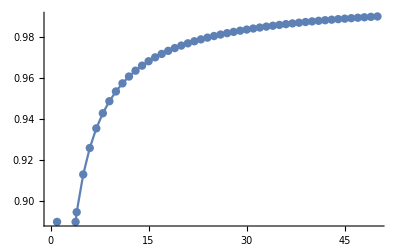

```mathematica
ListLinePlot[Map[Cn,Range[50]],Mesh->All,GridLines->{None,{1}},GridLinesStyle->Directive[AbsoluteThickness[6/2], ColorData[97,2]]]
```

Pri našem zaporedju Cn, vidimo, da je limita tudi enaka 1, vendar se številu 1 približuje bistveno počasneje kakor zaporedje Bn.
Preverimo še, če je limita res enaka 1.

```mathematica
Limit[n/Sqrt[n^2 +n],n->Infinity]
```

1

Vidimo, da je tudi tukaj limita 1. Sedaj zapišimo naše opazke.

-Graphics- Po izreku o sendviču od tod sledi: -Graphics-

Ker pa je limita našega zaporedja Bn in zaporedja Cn enaka 1, sedaj vemo, da je tudi limita An = 1.